```mathematica
length = 40 Quantity["Nanometers"];
width=3*length;
A = length*width;
Subscript[E, F]=-5 Quantity["Electronvolts"]//UnitConvert;
Subscript[E, C]=-4.7 Quantity["Electronvolts"];
Subscript[C, es]=0.1 Quantity["Femtofarads"];
q=Quantity["ElementaryCharge"];
Subscript[m, eff]=Quantity[9.1/2*10^-31,"Kilograms"];
Subscript[V, DS]=Quantity[0.3, "Volts"];
ℏ=Quantity["ReducedPlanckConstant"]//UnitConvert;
Subscript[k, B]=Quantity["BoltzmannConstant"]//UnitConvert;
β[T_]:=1/(Subscript[k, B] T);
Subscript[E, arr]=QuantityArray[Array[#&,10000,{-5,5}],"Electronvolts"]//UnitConvert;
Subscript[T, arr]=QuantityArray[{1,300},"Kelvins"];
Subscript[V, DSarr]=QuantityArray[Array[#&,100,{0,.5}],"Volts"];
Subscript[V, Garr]=QuantityArray[{.3,.35,.4,.45,.5},"Volts"];
Subscript[μ, s]=Subscript[E, F];
Subscript[μ, d][VDS_]:=Subscript[E, F]-q VDS;
g[E_]:=UnitStep[E];
f[E_,T_]:=1/(1+Exp[E β[T]]);
```

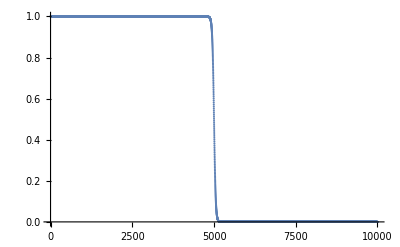

```mathematica
ListPlot[f[Subscript[E, arr],Subscript[T, arr][[2]]]]
```

```mathematica
f[Subscript[E, F],Subscript[T, arr][[2]]]
```

1/(1+1/ⅇ^(267029439/1380649))

```mathematica
UnitConvert[ℏ]
```

132521403/(400000000000000000000000000000000000000000 π) kg m^2/s